# Region Diagnostics: Time Series from CSV Export

Reads region_diagnostics.csv (visualizer's "Export Region Diagnostics", File menu) and plots ice strength, forcing/ice speeds, wind/current drag stress, and fractured fraction over time. Drag stress (traction, Pa) is computed at export time in the visualizer using the same quadratic drag law as the simulation (partition_kernel_update_nodes in kernels.cu), with the actual relative velocity between ice and wind/current (not an ice-stationary approximation) and mass-weighted over the masked region (zero-mass grid nodes don't contribute) -- see PPMainWindow::exportRegionDiagnostics_triggered in visualizer_mainwindow.cpp.

Edit the numbers in the Input cells directly and re-evaluate to try other values or a different CSV.

## Load Data

Expects region_diagnostics.csv next to this notebook. Column order (from PPMainWindow::exportRegionDiagnostics_triggered, visualizer_mainwindow.cpp):
frame, epoch_utc, datetime_utc, ice_strength_mean, ice_strength_max, wind_speed_mean, wind_speed_max, current_speed_mean, current_speed_max, ice_speed_mean, ice_speed_max, fractured_fraction, wind_drag_mean, wind_drag_max, current_drag_mean, current_drag_max

```mathematica
csvFile = FileNameJoin[{NotebookDirectory[], "region_diagnostics.csv"}];
rows = Rest[Import[csvFile, "CSV"]];  (* drop header row *)

epoch = rows[[All, 2]];
iceStrengthMean = rows[[All, 4]];
iceStrengthMax = rows[[All, 5]];
windSpeedMean = rows[[All, 6]];
windSpeedMax = rows[[All, 7]];
currentSpeedMean = rows[[All, 8]];
currentSpeedMax = rows[[All, 9]];
iceSpeedMean = rows[[All, 10]];
iceSpeedMax = rows[[All, 11]];
fracturedFraction = rows[[All, 12]];
windDragMean = rows[[All, 13]];
windDragMax = rows[[All, 14]];
currentDragMean = rows[[All, 15]];
currentDragMax = rows[[All, 16]];

tHours = (epoch - First[epoch])/3600.;  (* elapsed time since first exported frame, hours *)
```

## Plots

Each plot below is assigned to a named variable (plotXxx) so the Export Images section further down can save it, in addition to displaying it here.

### Ice strength

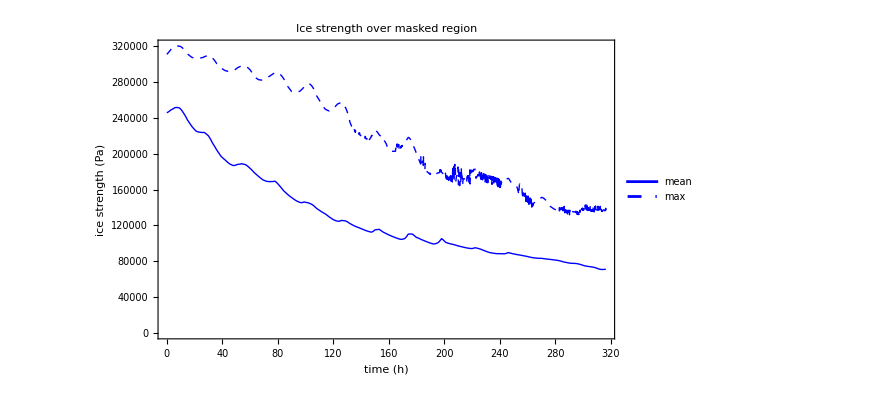

```mathematica
plotIceStrength = ListLinePlot[{Transpose[{tHours, iceStrengthMean}], Transpose[{tHours, iceStrengthMax}]},
  PlotLegends -> {"mean", "max"},
  PlotStyle -> {Directive[Blue, Thick], Directive[Blue, Thick, Dashed]},
  Frame -> True, FrameLabel -> {"time (h)", "ice strength (Pa)"},
  PlotLabel -> "Ice strength over masked region", ImageSize -> 650]
```

### Forcing and ice speeds (combined, for context)

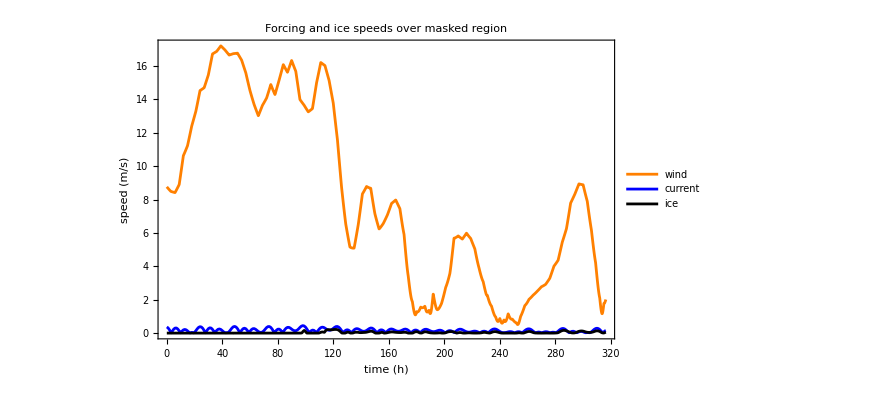

```mathematica
plotForcingSpeeds = ListLinePlot[{Transpose[{tHours, windSpeedMean}], Transpose[{tHours, currentSpeedMean}], Transpose[{tHours, iceSpeedMean}]},
  PlotLegends -> {"wind", "current", "ice"},
  PlotStyle -> {Directive[Orange, Thick], Directive[Blue, Thick], Directive[Black, Thick]},
  Frame -> True, FrameLabel -> {"time (h)", "speed (m/s)"},
  PlotLabel -> "Forcing and ice speeds over masked region", ImageSize -> 650]
```

### Ice speed (standalone)

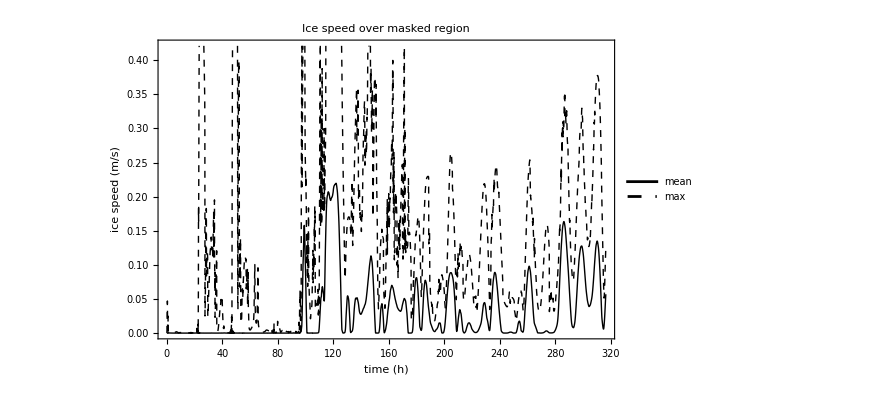

```mathematica
plotIceSpeed = ListLinePlot[{Transpose[{tHours, iceSpeedMean}], Transpose[{tHours, iceSpeedMax}]},
  PlotLegends -> {"mean", "max"},
  PlotStyle -> {Directive[Black, Thick], Directive[Black, Thick, Dashed]},
  Frame -> True, FrameLabel -> {"time (h)", "ice speed (m/s)"},
  PlotLabel -> "Ice speed over masked region", ImageSize -> 650]
```

### Wind/current drag stress

Mean is the magnitude of the mass-weighted mean drag vector over the masked region (so opposing-direction contributions partially cancel, as with a net regional force); max is the largest per-cell drag magnitude. No "total" line is shown -- the CSV stores wind and current drag magnitudes separately, without direction, so they can't be vector-summed into a true combined stress.

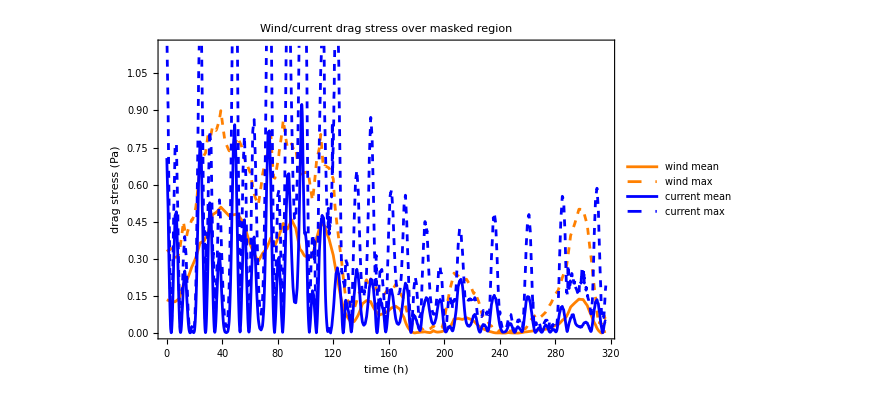

```mathematica
plotDragStress = ListLinePlot[{Transpose[{tHours, windDragMean}], Transpose[{tHours, windDragMax}], Transpose[{tHours, currentDragMean}], Transpose[{tHours, currentDragMax}]},
  PlotLegends -> {"wind mean", "wind max", "current mean", "current max"},
  PlotStyle -> {Directive[Orange, Thick], Directive[Orange, Thick, Dashed], Directive[Blue, Thick], Directive[Blue, Thick, Dashed]},
  Frame -> True, FrameLabel -> {"time (h)", "drag stress (Pa)"},
  PlotLabel -> "Wind/current drag stress over masked region", ImageSize -> 650]
```

### Fractured fraction

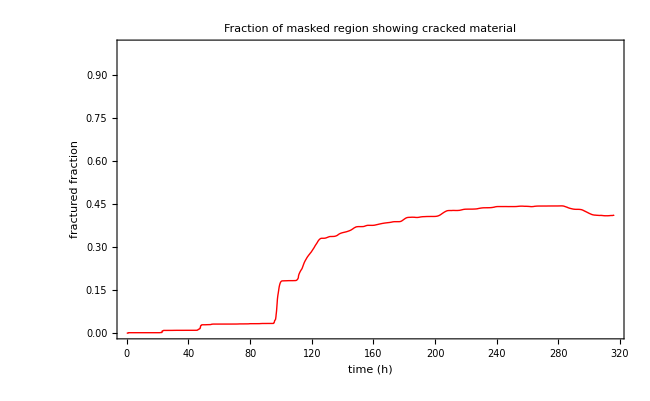

```mathematica
plotFracturedFraction = ListLinePlot[Transpose[{tHours, fracturedFraction}],
  PlotStyle -> Directive[Red, Thick],
  Frame -> True, FrameLabel -> {"time (h)", "fractured fraction"},
  PlotRange -> {0, 1}, PlotLabel -> "Fraction of masked region showing cracked material",
  ImageSize -> 650]
```

## Export Images

Saves the four requested plots as PNGs next to this notebook (not the combined "Forcing and ice speeds" one -- that's kept above for context only). Re-evaluate this cell any time after re-running the Plots section above.

```mathematica
figuresDir = NotebookDirectory[];
Export[FileNameJoin[{figuresDir, "drag_stress.png"}], plotDragStress, ImageResolution -> 300];
Export[FileNameJoin[{figuresDir, "fractured_fraction.png"}], plotFracturedFraction, ImageResolution -> 300];
Export[FileNameJoin[{figuresDir, "ice_strength.png"}], plotIceStrength, ImageResolution -> 300];
Export[FileNameJoin[{figuresDir, "ice_speed.png"}], plotIceSpeed, ImageResolution -> 300];
```